# NMRprocess 2

## Processing of NMR data Marcel Utz, University of Southampton February 2016

Package Implementation and Documentation

## Initialisation etc

```mathematica
BeginPackage["NMRProcess2`"];

NMRprocess::VersionNumber="2.0.0 " <> DateString[FileDate[FindFile["NMRProcess2.m"]]];

Print["NMR Processing
Version ", NMRprocess::VersionNumber, "
(c)2016 Marcel Utz
marcel.utz@southampton.ac.uk"];
```

## Notation and Data Structures

FID is the Head used for NMR data. Everything is stored in a Key/Value association. When an FID object is formatted for output, only a symbol is printed togehter with information on the dimensionality of the data.

```mathematica
Format[FID[assoc_]] := "-|NMR.." <> ToString[assoc[Dim] ] <> "--"
```

```mathematica
FID[<|Dim->2,TD->{1024,256}|>]
```

-|Fid..2--

The values inside the FID can be interrogated directly:

```mathematica
FID[q_][x_]:= q[x]
```

```mathematica
f=FID[<|Dim->1,Offset->20.0|>]
```

-|Fid..1--

```mathematica
f[Offset]
```

20.

## Read Bruker Data

```mathematica
ReadBruker[fname_, OptionsPattern[{ByteOrdering->-1,NumberFormat->"Integer32"}]] := 
		Module[{fid,fidcomplex,fidmatrix,l },
						
		(* Read Raw Data; we assume Integer32 numbers with Little Endian order unless specified otherwise*)
		
		fid=BinaryReadList[fname,OptionValue[NumberFormat],ByteOrdering->OptionValue[ByteOrdering]];
		l=Length[fid];
		fidcomplex=1.0fid[[1;;l;;2]] - 1.0 I fid[[2;;l;;2]] ;
		FID[<|Dim->1,data->fidcomplex,Points->l/2|>] 
];
```

```mathematica
fid1=ReadBruker["~/Dropbox/10/ser"]
```

-|Fid..1--

```mathematica
AddRaw[FID[q1_],FID[q2_]] := 
	Module[{qnew=q1},
		qnew[data]=q1[data]+q2[data];
		FID[qnew]
];
```

## Set Time Domain and other properties

The time domain data (and, after FT, the spectrum) is organised by referring to the directly acquired dimension first. This means, for a 3D spectrum, the data are stored in the order (t3 – t2 – t1). All lists of properties referring to the data (e.g., spectral width, sampling rate, etc) are ordered in the same way.

Internal data storage is organised as nested lists, with the innermost list corresponding to the acquired dimension. This has the advantage that with the above numbering convention, the t2 data is guaranteed to be at level 2, etc, in the internal storage.

```mathematica
SetTimeDomain[FID[q_],TD_List]:= 
	Module[{qnew=q},
		qnew[Dim]=Length[TD];
		qnew[Points]=TD;
		qnew[data] = ArrayReshape[q[data],Reverse[TD]];
		FID[qnew]
]
```

```mathematica
fid2=SetTimeDomain[fid1,{4096,256}]
```

-|Fid..2--

```mathematica
SetProp[FID[q_],key_->value_] := 
	Module[{qnew=q},
	qnew[key]=value;
	FID[qnew]
];

SetProp[F_FID, R_List] :=
	Module[{},
	Do[F=SetProp[F,next],{next,R}];
	F
];
```

```mathematica
SetProp[fid2,SpectralWidth->{20,90}]
```

-|Fid..2--

## Extracting Transients

Sometimes it is useful to extract single transients from a multi-dimensional FID by index.

```mathematica
ExtractTransient[FID[q_], n_List]:=Module[
	{qnew= <|Dim->1|>, selector= Join[n,{;;}]/.List->Sequence },

	qnew[data] = q[data][[selector]];
	qnew[Points] = Length[qnew[data]];
	qnew[Offset] = q[Offset][[1]];
	qnew[SpectralWidth] = q[SpectralWidth][[1]];
	FID[qnew]	
];
```

```mathematica
Join[{1,2,3},{;;}] /. List->Sequence
```

Sequence[1,2,3,1;;All]

## Processing

### Building Blocks, Operations on Flat Lists

```mathematica
FourierShift[data_?ListQ]:=
	Module[ {l},
		l=Length[data];
		Join[Take[data,-Floor[l/2]+1],Take[data,Floor[l/2]]]
	]
```

```mathematica
BaseLineCorrect[s_List,OptionsPattern[{Output->{1,-1},Regions->128,
									  Window->32,
									  KFactor->5,
									  InterpolationOrder->5}]]:=Module[{n=Length[s],nReg=OptionValue[Regions],win=OptionValue[Window],K=OptionValue[KFactor],order=OptionValue[InterpolationOrder],lreg,mindev,baslpoints,data,f},
(* Automatic Baseline correction, using the algorithm by S. Golotvin, A. Williams, J. Magn. Reson. 146 (1) (2000) 122–125. *)

(* Find minimum standard deviation *)
lreg=Floor[n/nReg];
mindev=Min[Table[StandardDeviation[s[[k;;k+lreg]]],{k,1,n-lreg,lreg}]];

(* select baseline points *)
baslpoints= Cases[Range[1+win/2,n-win/2,Round[win/10]],k_/;StandardDeviation[s[[k-win/2;;k+win/2]]]<K mindev] ;

data=Transpose[{baslpoints,s[[baslpoints]]}];

(* Fit polynomial to baseline points and subtract from data *)

f[x_]=Fit[data,Table[x^k,{k,0,order}],x];
OptionValue[Output][[1]]s+OptionValue[Output][[2]] f[Range[1,n]]

];
```

1-Dimensional linear prediction algorithm

```mathematica
LinPred[x_,p_,n_]:= 
	Module[{l=Length[x],a,R,r,xnew=x,k},
		r=Take[ListCorrelate[x,Conjugate[x],{1,1},0],p+1]/l;
		R=ToeplitzMatrix[Drop[r,-1]]; 
		a=Reverse[LinearSolve[R,Drop[r,1]]];
		Do[xnew=Append[xnew, a.Take[xnew,-p]],{k,1,n}];
	xnew
];
```

### Fourier Transformation

#### Vanilla 1D FT

```mathematica
FFT1D[FID[q_],OptionsPattern[{SI->1024,Phase0->Automatic,Phase1->0,Pivot->0,LeftShift->67,Apod->0.5}]]:= Module[
	{qnew=q,fid=q[data],apod,n,sf,pc1,pivot,si=OptionValue[SI],ls=OptionValue[LeftShift],p0=0,p1=0},

	If[q[Dim]≠ 1, Throw["FFT1D::Can only process 1D Data"]];

	If[OptionValue[Phase0]===Automatic, 
		p0=Arg[fid[[ls+1]]],
		p0=π OptionValue[Phase0]/180;
	];

	(* 1st order PC is measured in Degrees/SpectralWidth *)
	p1=π OptionValue[Phase1]/180;
	pivot=si/2;
	
	apod=Table[Exp[-OptionValue[Apod]π k / si],{k,1,si}]; 
	pc1=Table[Exp[I p1 (k-pivot)/si],{k,1,si}];

	sf = Reverse@BaseLineCorrect[FourierShift@Re[pc1*Fourier[apod*PadRight[Drop[fid,ls],si]] Exp[I p0]],Regions->32];
	qnew[spectrum]=sf;
	qnew[SpectSize]=si;

	FID[qnew]
]
```

#### StatesFFT2: HMQC spectra etc

```mathematica
StatesFFT2[FID[q_],OptionsPattern[{SI1->1024,SI2->1024,Phase1->0,Phase2->0,LeftShift->67}]] := Module[
	{qnew=q,
		sf2,sfa,sfb,si2=OptionValue[SI2],si1=OptionValue[SI1],
		p2=π OptionValue[Phase2]/180,p1=π OptionValue[Phase1]/180,
		ls=OptionValue[LeftShift],ser=q[data],apod2,apod1,n,m},

	{n,m}=Dimensions[ser];
	ser[[;;,1]] *= 0.5;
	apod2=PadRight[Table[0.5+0.5 Cos[π k / m],{k,1,m}],si2]; 
	(* sf2=Table[Reverse@BaseLineCorrect[FourierShift@Re[Fourier[apod2*PadRight[Drop[fid,ls],si2]] Exp[I p2]],Regions->32],{fid,ser}];*)
	sf2=Table[Reverse@FourierShift@Re[Fourier[apod2*PadRight[Drop[fid,ls],si2]] Exp[I p2]],{fid,ser}];
	sfa = Transpose[sf2[[1;; ;;2]] - I sf2[[2;; ;;2]]] ;
	
	sfa[[;;,1]]*=0.5;
	
	apod1= PadRight[Table[0.5+0.5 Cos[2 π k / n],{k,1,n/2}],si1]; 
	sfb = Table[Reverse@Re[Fourier[apod1*PadRight[fid,si1]] Exp[I p1]],{fid,sfa}];

	qnew[spectrum]=Transpose[sfb];
	qnew[SpectSize]={OptionValue[SI2],OptionValue[SI1]};

	FID[qnew]
	
]
```

```mathematica
spect=StatesFFT2[fid2,Phase2->-2.25,Phase1->-0.5,SI1->1024,SI2->4096]
```

-|Fid..2--

#### Covariance 2D Processing

>>Experimental<<

```mathematica
Covariance2D[FID[q_],OptionsPattern[{SI2->1024,Phase2->0,LeftShift->67}]] :=
	Module[{qnew=q,
		sf2,sfa,covm,si2=OptionValue[SI2],
		p2=OptionValue[Phase2],
		ls=OptionValue[LeftShift],ser=q[data],apod2,apod1,n,m},

	(* FT in the acquired domain *)
	
	ser[[;;,1]] *= 0.5;
	apod2=Table[Cos[π/2 k / si2],{k,1,si2}]; 
	sf2=Table[Reverse@BaseLineCorrect[FourierShift@Re[Fourier[apod2*PadRight[Drop[fid,ls],si2]] Exp[I p2]],Regions->32],{fid,ser}];
	
	(* sfa will contain ω2 traces in its rows *)
	sfa = sf2 ;

	(* Covariance Matrix *)
	covm = Transpose[sfa].sfa -  Transpose[{Total[sfa,{1}]}]. {Total[sfa,{1}]};

	qnew[spectrum]=MatrixPower[covm,1/2];
	qnew[SpectSize]={OptionValue[SI2],OptionValue[SI2]};

	FID[qnew]

]
```

Convert HSQCTOCSY spectrum into covariance TOCSY

```mathematica
CovHSQCTOCSY[FID[q_]] :=
	Module[{qnew=q,sfa},

		(* sfa will contain ω1 traces in its rows *)
		sfa=Transpose[q[spectrum]];

		(* Covariance Matrix *)
		covm = Transpose[sfa].sfa - 0. Transpose[{Total[sfa,{1}]}]. {Total[sfa,{1}]};

		qnew[spectrum]=MatrixPower[covm,1/2];
		qnew[SpectSize]=Dimensions[qnew[spectrum]];
		qnew[SpectralWidth]=q[SpectralWidth][[2]]{1,1};	
		qnew[Offset] =	q[Offset][[2]]{1,1};

	FID[qnew]
]
```

### Linear Prediction

Extend the FID data by ext points. ext is a list of the same dimension as the FID.

```mathematica
LinearPredict[FID[q_],ext_]:=
	Module[{qnew=q,sfa},
	  sfa=q[data] ;
	  
	FID[q]
] ;
```

## Index Math

This is intended for internal use only.

```mathematica
(* frq is a List of coordinates. First dimension is that of the data set (1D,2D,3D, etc).
   inner dimensions can be of any size; whole lists of coordinates can be processed at once
   in this way.
*)

Indx[q_,frq_]:=
	Module[{},
		If[Length[frq]≠ q[Dim], Throw["Indx::Dimension mismatch"] ];
		
		Floor[(0.5-(frq-q[Offset])/q[SpectralWidth])q[SpectSize]]
];

Frq[q_,indx_]:=
	Module[{},
		If[Length[indx]≠q[Dim], Throw["Frq::Dimension mismatch"] ];

		(0.5-indx/q[SpectSize])q[SpectralWidth]+q[Offset]
];
```

## Extracting Rows/Columns

We need some tools to access rows and columns in a 2D or 3D spectrum.

```mathematica
ExtractRow[FID[q_],s_Real]:= 
	Module[{qnew=q,spt,indx,a},
		qnew[Dim]=1;    (* This is always a 1D spectrum ! *)
		
		(* For now, we are assuming FID is a 2D spectrum. We'll deal with exceptions later. *)
		If[q[Dim]≠2, Throw["ExtractRow::Not a 2D spectrum"]];

		(* Compute row index closest to target value s
		   spt is the distance from the centre of the spectrum in points *)

		spt = q[SpectSize][[2]]*(s-q[Offset][[2]])/q[SpectralWidth][[2]] ;

		If[Abs[spt]>=q[SpectSize][[2]]/2, Throw["ExtractRow::Out of range."]];
		
		indx=Floor[q[SpectSize][[2]]/2]-Floor[spt]; 
		a=spt-Floor[spt];	
			
		qnew[spectrum] =  (1-a)q[spectrum][[indx-1]] + a  q[spectrum][[indx]] ;

		qnew[SpectralWidth]=q[SpectralWidth][[1]];
		qnew[Offset] = q[Offset][[1]];
		qnew[SpectSize] = q[SpectSize][[1]];

		FID[qnew]
] ;

SetAttributes[ExtractRow,{Listable}] ;

ExtractColumn[FID[q_],s_Real]:= 
	Module[{qnew=q,spt,indx,a},
		qnew[Dim]=1;    (* This is always a 1D spectrum ! *)
		
		(* For now, we are assuming FID is a 2D spectrum. We'll deal with exceptions later. *)
		If[q[Dim]≠2, Throw["ExtractColumn::Not a 2D spectrum"]];
		
		(* Compute row index closest to target value s
		   spt is the distance from the centre of the spectrum in points *)

		spt = q[SpectSize][[1]]*(s-q[Offset][[1]])/q[SpectralWidth][[1]] ;

		If[Abs[spt]>q[SpectSize][[1]]/2, Throw["ExtractColumn::Out of range."]];
		
		indx=Floor[q[SpectSize][[1]]/2]-Floor[spt]; 
		a=spt-Floor[spt];	
			
		qnew[spectrum] =  (1-a)q[spectrum][[;;,indx-1]] + a  q[spectrum][[;;,indx]] ;

		qnew[SpectralWidth]=q[SpectralWidth][[2]];
		qnew[Offset] = q[Offset][[2]];
		qnew[SpectSize] = q[SpectSize][[2]];

		FID[qnew]
]; 

SetAttributes[ExtractColumn,{Listable}] ;
```

```mathematica
spect[SpectSize]
```

{4096,1024}

```mathematica
spect=SetProp[spect,Offset,{-0.8,96.6}];
spect=SetProp[spect,SpectralWidth,{20,90}];
```

```mathematica
row=ExtractRow[spect,{98.,110.}]
```

{-|Fid..1--,-|Fid..1--}

### Crop Spectra

```mathematica
Crop[FID[q_],r_] := 
	Module[{qnew=q,indx,spn,lims,a,b},
	
	If[q[Dim] ≠ Length[r], Throw["Crop::Dimension mismatch"]];

	(* Translate range into indices *)
			
	indx = Indx[q,r]; 

	(* Select corresponding part of spectral data *)
	
	spn=Reverse[ indx /. {a_Integer,b_Integer}->Span[a,b] ] /. List->Sequence ; 
	qnew[spectrum] = q[spectrum][[spn]] ; 

	(* Adjust SpectralWidth, Offset, and SpectSize *)
	qnew[SpectSize] = Reverse[Dimensions[qnew[spectrum]]] ;
	
	lims= Frq[q,indx] ; 

	qnew[SpectralWidth] = lims /. {a_Real,b_Real}->a-b;
	qnew[Offset] = lims /. {a_Real,b_Real}->(b+a)/2;

	(* 1D spectra are a bit special *)

	If[q[Dim]==1,
		qnew[SpectralWidth] = First@qnew[SpectralWidth] ;
		qnew[SpectSize] = First@qnew[SpectSize] ;
		qnew[Offset] = First@qnew[Offset] ;
	];

	(* Done *)

	FID[qnew]
]
```

```mathematica
s1=ExtractRow[spect,98.3]
```

-|Fid..1--

```mathematica
Crop[s1,{{6.,2.}}]
```

-|Fid..1--

```mathematica
{spect[SpectralWidth], spect[Offset],spect[SpectSize]}
```

{{20,90},{-0.8,96.6},{4096,1024}}

```mathematica
small=Crop[spect,{{6.,2.},{100.,60.}}]
```

-|Fid..2--

```mathematica
{small[SpectralWidth], small[Offset],small[SpectSize]}
```

{{3.99902,39.9902},{4.00225,80.0326},{820,456}}

## Plotting

### 1D Plots

```mathematica
PlotNMR1D[FID[q_],opt:OptionsPattern[Options[ListLinePlot]]]:=
	Module[{d,max,min},

		If[q[Dim]≠1,Throw["PlotNMR1D::Not a 1D spectrum"] ];

		max=q[SpectralWidth]/2+q[Offset];
		min=-q[SpectralWidth]/2+q[Offset];
		ListLinePlot[q[spectrum],DataRange->{-max,-min},
						Ticks->{Charting`ScaledTicks[{-#1&,-#1&}],Automatic},
						Evaluate@FilterRules[{opt},Options[ListLinePlot]],
						Axes->{True,False}]
      
];

SetAttributes[PlotNMR1D,{Listable}] ;
```

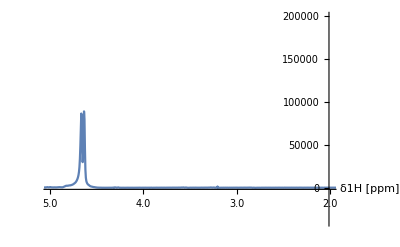

```mathematica
PlotNMR1D[ExtractRow[spect,98.3],PlotRange->{{-5,-2},2 10^4{-2,10}},AxesLabel->{"δ1H [ppm]",None},AxesOrigin->{Automatic,-2000}]
```

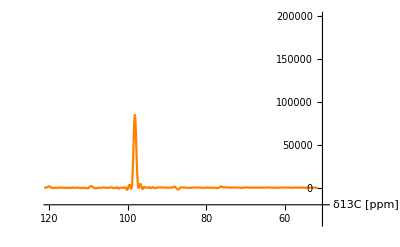

```mathematica
Rotate[PlotNMR1D[ExtractColumn[spect,4.65],PlotStyle->Orange,AxesLabel->{"δ13C [ppm]",None},PlotRange->{{-120,-50}, 2 10^4{-2,10}},AxesOrigin->{Automatic,-20000}],π/2]
```

It is also possible to Plot a whole list of traces at the same time:

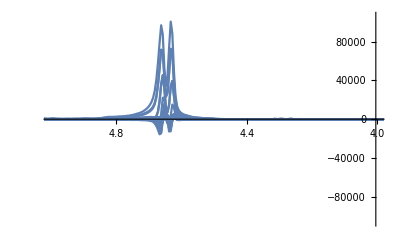

```mathematica
Show[ PlotNMR1D[ExtractRow[spect,Range[96.,100.,0.2]],PlotRange->{{-5,-4},Max[spect[spectrum]]{-1,1}} ]]
```

```mathematica
s1=ExtractRow[spect,98.3]
```

-|Fid..1--

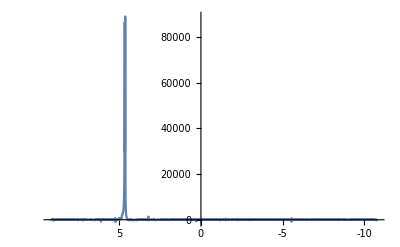

```mathematica
PlotNMR1D[s1,PlotRange->All,Axes->True]
```

```mathematica
sc=Crop[s1,{{4.8,4.4}}]
```

-|Fid..1--

```mathematica
sc[Offset]
```

4.60039

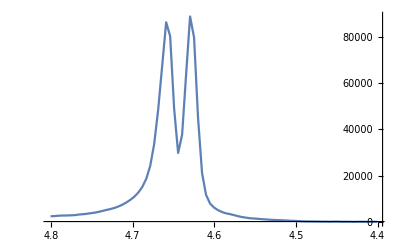

```mathematica
PlotNMR1D[sc,PlotRange->All]
```

```mathematica
Total[{{1,2,3,4},{5,6,7,8},{9,10,11,12}},{2}]
```

{10,26,42}

### 2D Contour Plots

```mathematica
NMRContourPlot[FID[q_],opt:OptionsPattern[Join[Options[ListContourPlot],{Gain->1}]] ]:= 
	Module[{},

		If[q[Dim]≠ 2,Throw["NMRContourPlot::Not a 2D spectrum"]];

		ListContourPlot[q[spectrum],
			DataRange->-q[SpectralWidth] {{-1/2,1/2},{-1/2,1/2}} - q[Offset] ,
			Evaluate@FilterRules[{opt},Options[ListContourPlot]],
			PlotRange -> Join[-q[SpectralWidth] {{-1/2,1/2},{-1/2,1/2}} - q[Offset],{All}] ,
			Contours-> 1./OptionValue[Gain] Max[q[spectrum]] Range[0.1,0.9,0.1],
			ContourShading->None,
			MaxPlotPoints->Automatic,
			PerformanceGoal->"Precision",
			FrameTicks->{{Charting`ScaledFrameTicks[{-#1&,-#1&}],Charting`ScaledTicks[{-#1&,-#1&}]},
				{Charting`ScaledTicks[{-#1&,-#1&}],Charting`ScaledFrameTicks[{-#1&,-#1&}]}}]

]
```

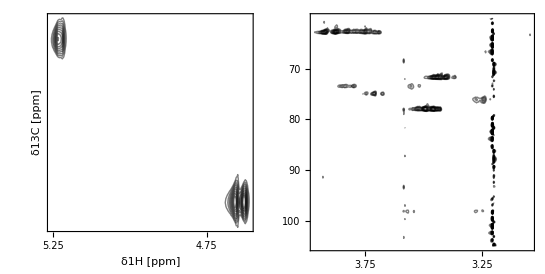

```mathematica
GraphicsGrid[ {{NMRContourPlot[Crop[spect,{{6.,4.5},{105,60}}],Contours->90000 Range[0.2,1,0.1] ,ImageSize->{Automatic,250} ,ImagePadding->{{50,0},{30,10}},
FrameLabel->{"δ1H [ppm]","δ13C [ppm]"}],
NMRContourPlot[Crop[spect,{{4.,2.5},{105,60}}],Contours->900 Range[0.2,1,0.1]  ,ImageSize->{Automatic,250},ImagePadding->{{50,0},{30,10}}] }}]
```

```mathematica
Export["~/Desktop/hmqc-2.png",%,ImageResolution->300]
```

~/Desktop/hmqc-2.png

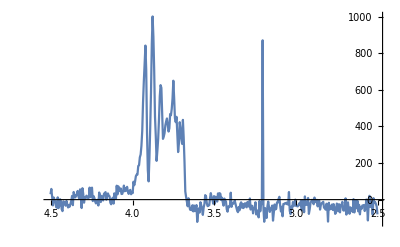

```mathematica
PlotNMR1D[Crop[ExtractRow[spect,62.7],{{4.5,2.5}}],PlotRange->All]
```

```mathematica
Keys[spect[[1]]]
```

{Dim,data,Points,spectrum,SpectSize,Offset,SpectralWidth}

## Projections

Project[ ] reduces the dimension of the spectrum by one, projecting the data along the dimension indicated (i.e., the indicated dimension is eliminated).

```mathematica
Project[FID[q_],{n_Integer},OptionsPattern[{Method->Total}]] :=
	Module[{qnew=q, clean1D := {xx_}->xx,
			projection=OptionValue[Method][#1,#2]&},

		If[n>q[Dim], Throw["Project::Dimension mismatch"]];
		If[q[Dim]==1,Return[Total[q[spectrum]]]];
		
		qnew[spectrum] = projection[q[spectrum],{n}];
		qnew[SpectSize] = Reverse[Dimensions[qnew[spectrum]]];
		qnew[Offset] = Drop[q[Offset],{-n}] /. clean1D ; (* minus sign: order convention *)
		qnew[SpectralWidth] = Drop[q[SpectralWidth],{-n}] /. clean1D;
		qnew[Dim]=q[Dim]-1;	
	
	FID[qnew]
]
```

### Contour Plot With Projections

```mathematica
NMRContourProjectionPlot[FID[q_],opt:OptionsPattern[Join[Options[ListContourPlot],
			{ProjectionStyle->{AbsoluteThickness[0.5],Gray},Gain->1}]] ]:= 
	Module[{padl=10,padr=50,padb=50,padt=2,contours,proj1,proj2},
	
	If[q[Dim]≠2,Throw["NMRContourProjectionPlot::Dimension mismatch"]];

	contours = NMRContourPlot[FID[q],
			ImagePadding->{{padl,padr},{padb,padt}},
			ImageSize->200+padl+padr, Evaluate@FilterRules[{opt},Join[Options[ListContourPlot],{Gain}]]] ;

	proj1 = PlotNMR1D[Project[FID[q],{1}],
			PlotRange->All,
			PlotStyle->OptionValue[ProjectionStyle],
			PlotRangePadding->Scaled[0.01],
			Axes->False,
			AspectRatio->1/4,
			ImagePadding->{{padl,padr},{2,0}},
			ImageSize->200+padl+padr ] ;
	
	proj2 = Show[PlotNMR1D[Project[FID[q],{2}],
					PlotRange->All,
					PlotStyle->OptionValue[ProjectionStyle],
					Axes->False,AspectRatio->4]  /. {a_Real,b_Real} -> {-b,a} ,
			PlotRange->All,
			PlotRangePadding->Scaled[0.01],
			ImagePadding->{{0,0},{padb,padt}},
			ImageSize->(200)/4] ;

	Graphics[{
		{Directive[White],Rectangle[{-1,-1},{1,1}]},
		Inset[proj1,{0,1}],
		Inset[proj2,{-1,0}],
		Inset[contours,{0,0}]
	}]
]
```

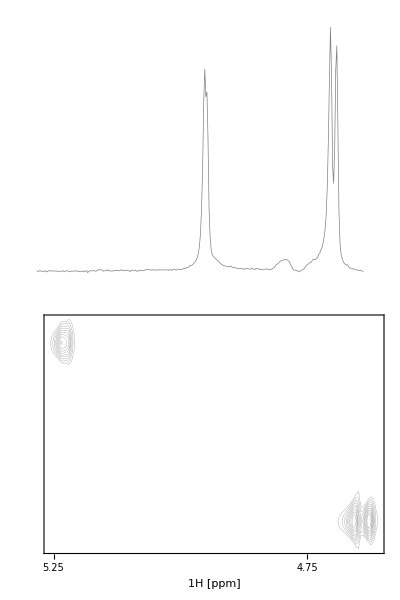

```mathematica
NMRContourProjectionPlot[sc,Contours->90000 Range[0.2,1,0.1],ContourStyle->{AbsoluteThickness[0.2]},GridLines->None,FrameLabel->{{"","13C [ppm]"},{"1H [ppm]",""}}]
```

```mathematica
sc2=Crop[spect,{{4.2,3.3},{80.,60.}}]
```

-|Fid..2--

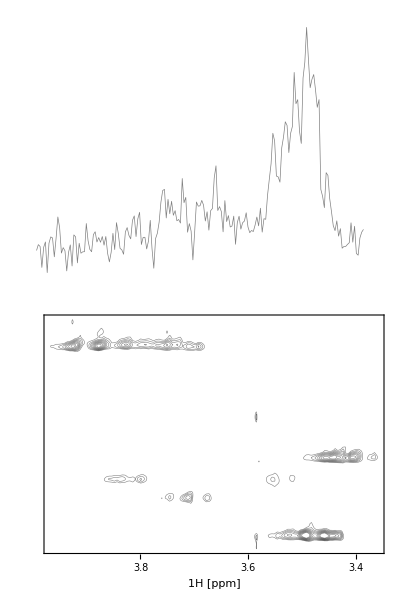

```mathematica
NMRContourProjectionPlot[sc2,Contours->900 Range[0.2,1,0.1],ContourStyle->{AbsoluteThickness[0.4]},GridLines->None,FrameLabel->{{"","13C [ppm]"},{"1H [ppm]",""}}]
```

```mathematica
Export["~/Desktop/test.pdf",%]
```

~/Desktop/test.pdf

## Cleanup

```mathematica
EndPackage[]
```